# Density data plotting code

## Version: 1.0.0

## Directory setting

```mathematica
currentDir=NotebookDirectory[];
SetDirectory[currentDir];
datadir="../../data/density/";
simdir="../simulation/";
importdir=simdir;
```

## File import

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
filename="2021-05-11-02/data";
hdf5File=Import[ToString@Row@{importdir,filename,".hdf5"},"Data"];
```

```mathematica
imstack=hdf5File⟦1,1;;18000⟧;
Histogram@imstack⟦;;,3,1⟧
```

```mathematica
imstack +=hdf5File⟦1,1;;18000⟧;
Histogram@imstack⟦;;,3,1⟧
```

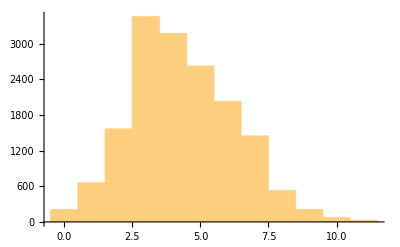

```mathematica
simstack=hdf5File⟦1,1;;80000;;5,1,;;,;;⟧;
imstack=simstack;
Histogram@imstack⟦;;,3,1⟧
```

```mathematica
imstack⟦1⟧
```

## Parameters

```mathematica
bincount=12;
antcount=200;
normfactor=1;
```

## Time integration

```mathematica
(*For stacking multiple datafiles only*)
imstack +=hdf5File⟦1,1;;18000⟧;
```

### aaa

```mathematica
imstack=imstack-Min[imstack];
squish=imstack⟦1⟧;
Do[
squish+=imstack⟦i⟧;
,{i,2,Length[imstack]}]
squish/=Length[imstack];
totalantness=antcount Length[imstack];
```

```mathematica
squished=(antcount squish)/(Total@Total@squish);
```

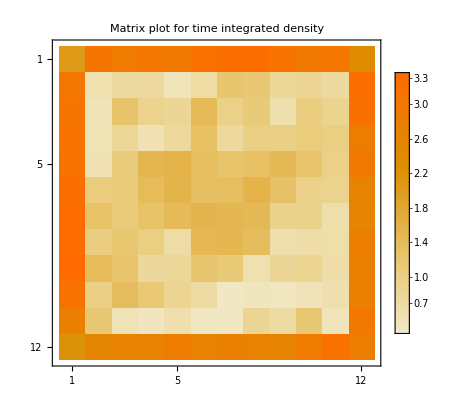

```mathematica
a=Show[MatrixPlot[squished,PlotLegends->Automatic,PlotLabel->"Matrix plot for time integrated density"]]
```

```mathematica
Export[ToString@Row@{filename,"out.png"},a];
```

```mathematica
(*antcount/Total[imstack⟦i⟧,{1,2}]*)
```

```mathematica
Directory[]
```

```mathematica
diff=thing-squish;out2=Show[MatrixPlot[diff,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export[ToString@Row@{filename,"diff.png"},out2]
```

```mathematica
thingr=Reverse[thing,{1,2}];
```

```mathematica
MatrixPlot@(thingr-thing)
```

```mathematica
MatrixPlot@thing
```

```mathematica
rat=diff/squish;
```

```mathematica
out3=Show[MatrixPlot[rat,PlotLegends->Automatic,ColorFunction->"TemperatureMap",Mesh->True,MeshStyle->Thin,PlotLabel->"Matrix plot for time integrated density (Tracking)"]]
```

```mathematica
Export[ToString@Row@{filename,"perdiff.png"},out3]
```

```mathematica
MatrixPlot[150 hdf5File⟦1,-1⟧,PlotLegends->Automatic]
```

## Vexation

```mathematica
stackedimstack=imstack;
```

```mathematica
norm=ConstantArray[0,{bincount,bincount}];
```

```mathematica
Do[Do[
norm⟦j,k⟧=Sum[imstack⟦i,j,k⟧/antcount,{i,1,Length[imstack]}]
,{j,1,bincount}],{k,1,bincount}]
```

```mathematica
vexation=-Log[squished norm ];
```

```mathematica
prob=ConstantArray[0,{bincount,bincount}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n vexation⟦i,j⟧]/(norm⟦i,j⟧ Factorial[n]);
,{i,1,bincount}],
{j,1,bincount}]
```

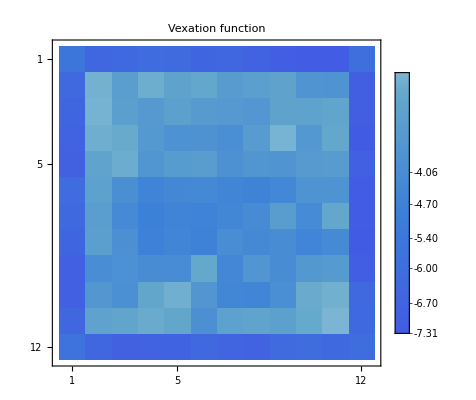

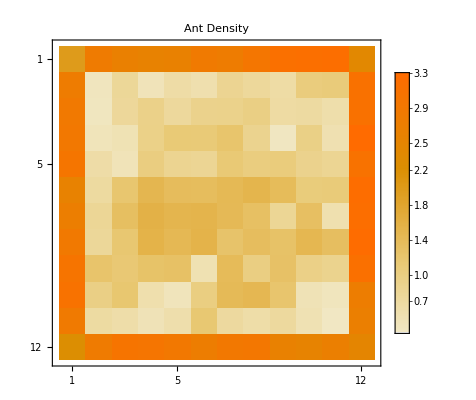

```mathematica
MatrixPlot[vexation,PlotLegends->Automatic,PlotLabel->"Vexation function"]
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Ant Density"]
```

## Symmetrify

```mathematica
halfa=vexation⟦1;;4⟧;
```

```mathematica
halfb=vexation⟦5;;8⟧;
```

```mathematica
MatrixPlot@Reverse[halfa]
```

```mathematica
halfsum=halfa+Reverse[halfb];
```

```mathematica
quartera=halfsum⟦;;,1;;4⟧;
quarterb=halfsum⟦;;,5;;8⟧;
```

```mathematica
quartersum=quartera+Reverse[quarterb,2];
```

```mathematica
unfold=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfold⟦i,j⟧=quartersum⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

```mathematica
halfa1=norm⟦1;;4⟧;
```

```mathematica
halfb1=norm⟦5;;8⟧;
```

```mathematica
MatrixPlot@Reverse[norm]
```

```mathematica
halfsum1=halfa1+Reverse[halfb1];
```

```mathematica
quartera1=halfsum1⟦;;,1;;4⟧;
quarterb1=halfsum1⟦;;,5;;8⟧;
```

```mathematica
quartersum1=quartera1+Reverse[quarterb1,2];
```

```mathematica
unfoldnorm=ConstantArray[0,{8,8}];
```

```mathematica
Do[Do[
a=Mod[Abs[(-9Quotient[i,5])+Mod[i,5]],5];
b=Mod[Abs[(-9Quotient[j,5])+Mod[j,5]],5];
unfoldnorm⟦i,j⟧=quartersum1⟦a,b⟧/4.
,{i,1,8}],
{j,1,8}]
```

```mathematica
MatrixPlot[unfold,PlotLegends->Automatic,PlotLabel->"Vexation symmetrized"]
```

```mathematica
prob=ConstantArray[0,{8,8}];
n=1;
```

```mathematica
Do[
Do[
prob⟦i,j⟧=Exp[-n unfold⟦i,j⟧]/(unfoldnorm⟦i,j⟧ Factorial[n]);
,{i,1,8}],
{j,1,8}]
```

```mathematica
MatrixPlot[prob,PlotLegends->Automatic,PlotLabel->"Density Symmetrized"]
```

## Frustration

```mathematica
(*Needs large number of ants*)
```

```mathematica
(*probf=HistogramList[timesquish,{0.001},"PDF"];*)
probf=HistogramList[normfactor Flatten@imstack,{1},"PDF"];
probf⟦1⟧=Drop[probf⟦1⟧,-1];
```

```mathematica
frustration[n_,pn_]:=-vexation n - Log[norm Factorial[n] pn];
```

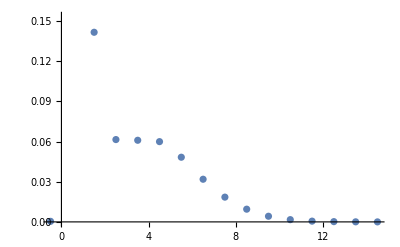

```mathematica
ListPlot@(probfᵀ)
```

```mathematica
frustrray=ConstantArray[0,Length[probf⟦1⟧]];
Do[
frustrray⟦n⟧={probf⟦1,n⟧,Mean@Flatten@frustration[probf⟦1,n⟧,probf⟦2,n⟧]};
,{n,1,Length[frustrray]}]
```

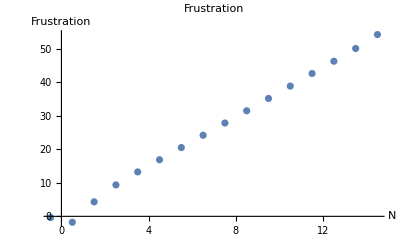

```mathematica
ListPlot[frustrray,PlotLabel->"Frustration", AxesLabel->{"N","Frustration"}]
```

```mathematica
Module[
(* Set local parameters for plotting *)
{data=normfactor Flatten@imstack,
samplesize=0,
flatten=True,
axesLabel={"Number of ants","PDF"},
angularticks=True,
range, ticks, err, dist, hist, len, errors,
bincounts, binwidth, copy, temp},
bincounts=Ceiling@Max@data;
(* Modify structure of data and set up plotting parameters *)
Do[
samplesize+=Length[data⟦i⟧]
,{i,1,Length[data]}];
If[samplesize==0,
samplesize=Length[data]];
If[flatten,data=Flatten[data]];
range={Min[data],Max[data]};
If[angularticks,
ticks={Range[0,Max[data],1],Automatic},
ticks=Automatic];
err={};
Do[
AppendTo[err,ErrorBar[1./(range⟦2⟧-range⟦1⟧),1/Sqrt[samplesize]]];
,{n,1,10}];

(* Generate basic plots using the configs *)
dist=SmoothKernelDistribution[data];
avHistogram=Histogram[data,bincounts,"PDF",AxesLabel->axesLabel,PlotRange->Full,ImageSize->Large,Ticks->ticks,GridLines->Automatic,PlotLabel->"Histogram of Angular Velocity folded in half"];
avPDF=Plot[PDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel distribution of Angular Velocity near center"];
avCDF=Plot[CDF[dist,x],{x,0,π},PlotRange->Full,AxesLabel->axesLabel,ImageSize->Large,Ticks->ticks,PlotLabel->"Kernel PDF of Angular Velocity near center"];

(* Generate histogrambins for further analysis *)
temp={};
hist=HistogramList[data,{Max[data]/bincounts},"PDF"];
len=Length[hist⟦1⟧];
errors={};
Do[
AppendTo[temp,(hist⟦1,i⟧+hist⟦1,i+1⟧)/2.];
binwidth=Max[data]/bincounts;
AppendTo[errors,ErrorBar[binwidth/2.,Sqrt[hist⟦2,i⟧(1-hist⟦2,i⟧binwidth)/(Length[data]binwidth)]]]
,{i,1,Length[hist⟦2⟧]}];
hist={temp,hist⟦2⟧};
copy=histᵀ;
coopy=hist;
hist=Partition[Riffle[histᵀ,errors],2];
(* Generate Error analysis and symmetry analysis plots *)
antcountErrorPlot=ErrorListPlot[hist,PlotRange->{{0,1.05(Max[data]+1)},Full},AxesLabel->axesLabel,PlotLabel->"Histogram of Ant count (With error bars)",PlotStyle->PointSize[0]];(*mirror=[-copyᵀ⟦1⟧,Reverse[copyᵀ⟦2⟧];*)
avSym=ListPlot[{{ -copyᵀ⟦1⟧,copyᵀ⟦2⟧}ᵀ,copy},PlotRange->{{0,Automatic},Full},PlotLabel->"Left-Right comparison for angular velocity distribution",PlotLegends->{"Left","Right"},ImageSize->700,Ticks->ticks,AxesLabel->{"Angular velocity (rad/s)", "PDF"}];
];
```

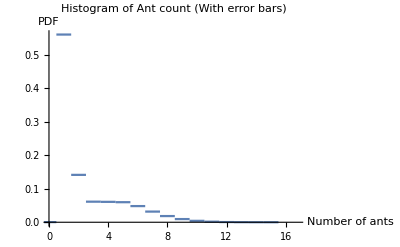

```mathematica
antcountErrorPlot
```

```mathematica
m=1;
frustprob=1/(m!)1/norm(Exp[-vexation]^m Exp[-frustrray⟦m,2⟧]);
```

```mathematica
frustrray
```

{{-0.5,-0.359611},{0.5,-1.76304},{1.5,4.32579},{2.5,9.36149},{3.5,13.2351},{4.5,16.8656},{5.5,20.4945},{6.5,24.1565},{7.5,27.8031},{8.5,31.4471},{9.5,35.1243},{10.5,38.809},{11.5,42.5646},{12.5,46.2136},{13.5,50.0113},{14.5,54.1636}}

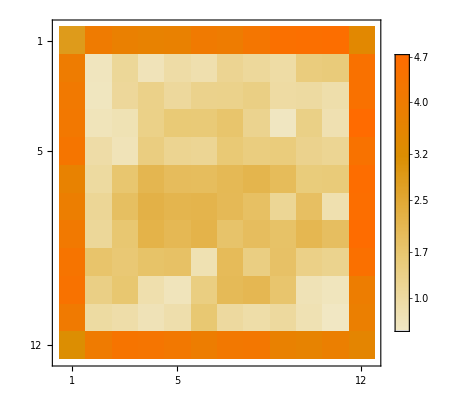

```mathematica
MatrixPlot[frustprob,PlotLegends->Automatic]
```